# Rotations of Moment of Inertia Tensor

## using Quaternions

Mikica B Kocic, 2012-04-22, v0.3

There is a wonderful connection between complex numbers (and quaternions, as their extension) and geometry in which, translations correspond to additions, rotations and scaling to multiplications, and reflections to conjugations.

However, the beauty of describing spatial rotations with quaternions is shadowed by an expression like:

(1-2 (y^2+z^2) | 2 x y-2 w z | 2 w y+2 x z
2 x y+2 w z | 1-2 (x^2+z^2) | 2 y z-2 w x
2 x z-2 w y | 2 w x+2 y z | 1-2 (x^2+y^2))·
·𝒥·(1-2 (y^2+z^2) | 2 x y-2 w z | 2 w y+2 x z
2 x y+2 w z | 1-2 (x^2+z^2) | 2 y z-2 w x
2 x z-2 w y | 2 w x+2 y z | 1-2 (x^2+y^2))^T

which actually represents such simple transformation as the rotation of moment of inertia tensor using quaternions [2].

The purpose of this document is to express spatial rotations of a moment of inertia tensor in the pure quaternionic form and to highlight the algebraical meaning behind such rotations by proving some interesting theorems.

## Conventions and Definitions

Load quaternions package (see Quat.nb for the annotated source code)

```mathematica
Get[ "Quat.m",Path->{ NotebookDirectory []  } ];
```

#### Conventions

In this document, matrices, vectors and matrix representation of quaternions are shown in uppercase font (roman-bold font in text) and quaternions and other numbers are shown in lowercase font (italic font in text). Since the symbol I in Mathematica is used for imaginary unit, the selected symbol for moment of inertia is the uppercase script J i.e. 𝒥. The identity matrix is suffixed with a number of dimensions, i.e. I4 represents the identity matrix in ℝ^4.

Matrices 4×4 originated from quaternions may be geometrically partitioned into scalar (real), vector (pure imaginary) and cross-product parts [3]. Such partitions are visualized using row and column divider lines throughout this document:

(scalar | □ | vector | □
□ | □ | □ | □
vector^ᵀ | □ | cross product  | □
□ | □ | □ | □)

#### General symbols and variables used in theorems (definitions)

Hamilton's quaternions q, q_1 and q_2 with real number components (but not with complex number components as biquaternions; see definition of default $Assumptions bellow):

```mathematica
q=𝒬[ w,x,y,z ];
```

```mathematica
q1=𝒬[ w1,x1,y1,z1 ];
```

```mathematica
q2=𝒬[ w2,x2,y2,z2 ];
```

Identity matrix I4 in ℝ^4:

```mathematica
I4=IdentityMatrix[4];
```

Common ℝ^4 matrices A and B:

```mathematica
A = ({{Aww, Awx, Awy, Awz}, {Axw, Axx, Axy, Axz}, {Ayw, Ayx, Ayy, Ayz}, {Azw, Azx, Azy, Azz}});
```

```mathematica
B = ({{Bww, Bwx, Bwy, Bwz}, {Bxw, Bxx, Bxy, Bxz}, {Byw, Byx, Byy, Byz}, {Bzw, Bzx, Bzy, Bzz}});
```

Symmetrical ℝ^4 matrix representing moment of inertia tensor 𝒥:

```mathematica
𝒥=({{1, 0, 0, 0}, {0, Ixx, Ixy, Ixz}, {0, Ixy, Iyy, Iyz}, {0, Ixz, Iyz, Izz}});
```

Default assumption used for all asserted statements and expressions in this notebook is that previously defined entities q, q_1, q_2, A, B and 𝒥 are on field of ℝ, i.e. that their components are elements in ℝ:

```mathematica
$Assumptions = Flatten@{ ToList/@{ q, q1, q2 },A,B,𝒥}∈Reals;
```

### Different Types of Multiplications

The ordirary notation for multiplication in Mathematica is

A . B		multiplication between matrices ("dot" multiplication)
a × b		cross-product between 3D vectors
p ** q		quaternion multiplication (both in Quat.m and Mathematica Quaternions package)

Beside the ordinary notation for multiplication, this document also introduces the following notation based on the center dot (·) operator.

A · B		:= multiplication between matrices
p · q		:= quaternion multiplication
q · A		:= column-wise quaternion-matrix multiplication

Note that the center dot operator in Mathematica is without built-in meaning.

#### Matrix multiplication

Define center dot operator A · B as matrix multiplication (otherwise, Mathematica uses plain dot "." for matrix multiplications).

```mathematica
CenterDot[ m__ ?MatrixQ ] := Dot[ m ]
```

#### Quaternion multiplication

Mathematica uses non-commutative multiply (**) operator as symbol for quaternion multiplication. The Quat.m package and this document follow this convention. Here we define also the center dot operator as symbol for quaternion multiplication, just for convinience and esthetics

```mathematica
CenterDot[ q__ ?𝒬Q ] := NonCommutativeMultiply[ q ]
```

#### Column-wise (or horizontal) quaternion-matrix multiplication

Let us now define multiplication between quaternion q and matrix M, where it is assumed that matrix is a row vector of quaternions in columns, i.e. M=(q_1 | q_2 | ... | q_n), so that quaternion multiplication is done between q and q_j in every column j.

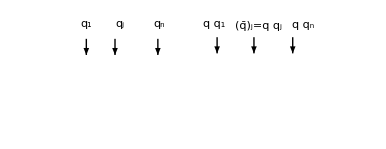

Since the quaternion multiplication is not commutative, there are several cases to distinguish:

a) Left multiplication q·M, where a quaternion in each column in M is multiplied by the quaternion q from the left:

```mathematica
CenterDot[ q_?𝒬Q,mat_?MatrixQ ]:=Transpose@
Table[
ToList[ q · To𝒬@mat_⟦All,j⟧ ],{j,1,Dimensions[mat]_⟦2⟧}
]
```

b) Right multiplication M·q, where a quaternion in each column in M is multiplied by the quaternion q from the right:

```mathematica
CenterDot[ mat_?MatrixQ,q_?𝒬Q ]:=Transpose@
Table[
ToList[ To𝒬@mat_⟦All,j⟧ · q ],{j,1,Dimensions[mat]_⟦2⟧}
]
```

c) Compound multiplication from both sides p·M·q, where multiplication of each column in M by the quaternion p from the left and q from the right:

```mathematica
CenterDot[ q1_?𝒬Q,mat_?MatrixQ,q2_?𝒬Q ]:=Transpose@
Table[
ToList[ q1 · To𝒬@mat_⟦All,j⟧ · q2 ],{j,1,Dimensions[mat]_⟦2⟧}
]
```

The multiplication between a quaternion and a matrix is associative, i.e. it holds:

q_1·M·q_2==q_1·(M·q_2)==(q_1·M)·q_2

which is proved as a theorem in the following sections.

Note that for a single column matrix M, the multiplication between a quaternion and a matrix falls back to an ordinary quaternion multiplication.

#### Row-wise (or vertical) quaternion-matrix multiplication

Row-wise quaternion-matrix multiplication can be defined by transposing matrices and using column-wise multiplication:

( q_1·M^ᵀ·q_2 )^ᵀ

#### Conj[] matrix operator

Conj[] operator conjugates only the vector part of the matrix, but not the scalar and the cross product parts:

```mathematica
Conj[ q_?MatrixQ ]:=
({{q_⟦1,1⟧, -q_⟦1,2⟧, -q_⟦1,3⟧, -q_⟦1,4⟧}, {-q_⟦2,1⟧, q_⟦2,2⟧, q_⟦2,3⟧, q_⟦2,4⟧}, {-q_⟦3,1⟧, q_⟦3,2⟧, q_⟦3,3⟧, q_⟦3,4⟧}, {-q_⟦4,1⟧, q_⟦4,2⟧, q_⟦4,3⟧, q_⟦4,4⟧}})
```

Note that Conj[] is not a conjugate of a quaternion! The conjugate of a quaternion corresponds to the plain transpose of the matrix.

#### Idea behind quaternion-matrix multiplication

Basic idea behind the quaternion-matrix multiplication comes from an expression:

```mathematica
Assert[
𝒬[ 1, 0, 0, 0 ] == q·𝒬[ 1, 0, 0, 0 ]·SuperStar[q],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

for which it is assumed to be also valid when transforming identity matrix I4 that is equvalent representation of the quaternion 𝒬[ 1, 0, 0, 0 ] in matrix form, i.e. that there should be kind of multiplication where:

```mathematica
Assert[
Transpose[({{1, 0, 0, 0}})] == q · Transpose[({{1, 0, 0, 0}})] · SuperStar[q],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

## Theorems

#### Quaternion-matrix multiplication

Quaternion multiplication associativity (sanity-check):

```mathematica
q1·q·q2 == q1·( q·q2) == (q1·q)·q2 //Assert
```

⊢ True ▮

Quaternion-matrix multiplication associativity theorems:

```mathematica
q1·A·q2 == q1·( A·q2 ) == ( q1·A )·q2 //Assert
```

⊢ True ▮

```mathematica
q·A·SuperStar[q] == ( q·A )·SuperStar[q] //Assert
```

⊢ True ▮

```mathematica
q·A·SuperStar[q] == q·( A·SuperStar[q] ) //Assert
```

⊢ True ▮

```mathematica
Transpose[( q·I4 )] == SuperStar[q]·I4 //Assert
```

⊢ True ▮

```mathematica
Transpose[( I4·q )] == I4·SuperStar[q]  //Assert
```

⊢ True ▮

```mathematica
(q·I4)·A == q·A//Assert
```

⊢ True ▮

```mathematica
(I4·q)·A == A·q //Assert
```

⊢ True ▮

```mathematica
(q1·I4)·(I4·q2) == q1·I4·q2 //Assert
```

⊢ True ▮

```mathematica
(I4·q2)·( (q1·I4)·A )== (q1·A)·q2 == q1·A·q2 //Assert
```

⊢ True (after Simplify) ▮

```mathematica
(I4·q2)·(q1·I4)·A== q1·A·q2 ∧
(I4·q2)·(q1·I4)·A== q1·A·q2 ∧
(q1·I4)·(I4·q2)·A== q1·A·q2 ∧
(q1·I4·q2)·A== q1·A·q2  //Assert
```

⊢ True (after Simplify) ▮

Conjugations of quaternion-matrix multiplications:

```mathematica
Conj[ q·A ] == Conj[A]·SuperStar[q]  //Assert
```

⊢ True ▮

```mathematica
Conj[ A·q ] == SuperStar[q]·Conj[A] //Assert
```

⊢ True ▮

```mathematica
Conj[ q1·A·q2] ==Conj[ q1·(A·q2)] == Conj[A·q2]·SuperStar[q1] == SuperStar[q2]·Conj[A]·SuperStar[q1]//Assert
```

⊢ True (after Simplify) ▮

```mathematica
Conj[ q·A·SuperStar[q]] == q·Conj[A]·SuperStar[q]//Assert
```

⊢ True (after Simplify) ▮

#### Left and right rotation matrices

Because the quaternion multiplication is bilinear, it can be expressed in a matrix form, and in two different ways ([1]). Multiplication on the left qp gives L_q·p where p is now treated as a 4-dimensional column vector p and multiplication on the right pq gives p ·R_q.

Let us define L_q and R_q as quaternion-multiplication with identity matrix:

```mathematica
ClearAll[ L,R,Q ]
```

```mathematica
Subscript[L, q_]:= q·I4
Subscript[R, q_]:= I4·q
Subscript[Q, q_]:=Subscript[L, q]·Subscript[R, SuperStar[q]]
```

Proof that the quaternion multiplication can be decomposed into L&R matrix parts and that L_q R_(q^*)p corresponds to qp q^* :

```mathematica
Assert[
Subscript[L, q]·Subscript[R, SuperStar[q]]·ToVector[q1]== ToVector[ q·q1·SuperStar[q] ],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

#### Properties of L, R and Q matrices

```mathematica
Subscript[L, SuperStar[q]]==Transpose[(Subscript[L, q])]  //Assert
```

⊢ True ▮

```mathematica
Subscript[R, SuperStar[q]]==Transpose[(Subscript[R, q])] //Assert
```

⊢ True ▮

```mathematica
( q·Subscript[R, SuperStar[q]] )·A==q·( Subscript[R, SuperStar[q]]·A )==(Subscript[L, q]·A )·SuperStar[q] //Assert
```

⊢ True (after Simplify) ▮

```mathematica
Subscript[Q, q]==Subscript[L, q]·Subscript[R, SuperStar[q]]==Transpose[(Transpose[Subscript[R, SuperStar[q]]]·Transpose[Subscript[L, q]])]==Transpose[(Subscript[R, q]·Subscript[L, SuperStar[q]])]==Subscript[R, SuperStar[q]]·Subscript[L, q] //Assert
```

⊢ True ▮

```mathematica
Subscript[Q, SuperStar[q]]==Subscript[R, q]·Subscript[L, SuperStar[q]]==Subscript[L, SuperStar[q]]·Subscript[R, q] //Assert
```

⊢ True ▮

```mathematica
Subscript[Q, q]·Subscript[Q, SuperStar[q]]==(|q|)^4 I4//Assert
```

⊢ True (after Simplify) ▮

```mathematica
Conj[Subscript[L, q]·A ]·SuperStar[q]==Conj[ q·(Subscript[L, q]·A) ] //Assert
```

⊢ True (after Simplify) ▮

```mathematica
Conj[Subscript[L, q]·A ]·SuperStar[q]==Conj[Subscript[L, q]·A]·SuperStar[q] //Assert
```

⊢ True ▮

#### L & R matrices components

```mathematica
Grid@{ 
{ "L_q", "L_(q^*)", "R_q", "R_(q^*)" },
{ Subscript[L, q] //QForm, Subscript[L, SuperStar[q]] //QForm, Subscript[R, q] //QForm, Subscript[R, SuperStar[q]] //QForm }
}
```

L_q | L_(q^*) | R_q | R_(q^*)
(w | -x | -y | -z
x | w | -z | y
y | z | w | -x
z | -y | x | w) | (w | x | y | z
-x | w | z | -y
-y | -z | w | x
-z | y | -x | w) | (w | -x | -y | -z
x | w | z | -y
y | -z | w | x
z | y | -x | w) | (w | x | y | z
-x | w | -z | y
-y | z | w | -x
-z | -y | x | w)

#### Rotation matrix Q components

```mathematica
Grid@{ 
{ "Q_q == L_q·R_(q^*) == R_(q^*)·L_q", "Q_(q^*) == L_(q^*)·R_q == R_q·L_(q^*)" },
{ Simplify[ Subscript[Q, q], Assumptions->(|q|)^2==1 ] //QForm,
 Simplify[ Subscript[Q, SuperStar[q]], Assumptions->(|q|)^2==1 ] //QForm }
}
```

Q_q == L_q·R_(q^*) == R_(q^*)·L_q | Q_(q^*) == L_(q^*)·R_q == R_q·L_(q^*)
(1 | 0 | 0 | 0
0 | 1-2 y^2-2 z^2 | 2 x y-2 w z | 2 (w y+x z)
0 | 2 (x y+w z) | 1-2 x^2-2 z^2 | -2 w x+2 y z
0 | -2 w y+2 x z | 2 (w x+y z) | 1-2 x^2-2 y^2) | (1 | 0 | 0 | 0
0 | 1-2 y^2-2 z^2 | 2 (x y+w z) | -2 w y+2 x z
0 | 2 x y-2 w z | 1-2 x^2-2 z^2 | 2 (w x+y z)
0 | 2 (w y+x z) | -2 w x+2 y z | 1-2 x^2-2 y^2)

#### Shoemake's rotation matrix from quaternion

Classical Shoemake's form of the rotation matrix from a quaternion is given as (a transformation matrix based on the Cayley-Klein parameters; see [2]):

```mathematica
RotationMatrix4[ q ] //QForm
```

(1 | 0 | 0 | 0
0 | 1-2 (y^2+z^2) | 2 x y-2 w z | 2 w y+2 x z
0 | 2 x y+2 w z | 1-2 (x^2+z^2) | -2 w x+2 y z
0 | -2 w y+2 x z | 2 w x+2 y z | 1-2 (x^2+y^2))

#### Scalar, vector and cross-product parts of L&R matrices

Scalar part:

```mathematica
1/2(Subscript[L, q]+Subscript[L, SuperStar[q]])==1/2(Subscript[R, q]+Subscript[R, SuperStar[q]])==({{w, 0, 0, 0}, {0, w, 0, 0}, {0, 0, w, 0}, {0, 0, 0, w}}) // Assert
```

⊢ True ▮

Vector part:

```mathematica
1/2(Subscript[L, SuperStar[q]]-Subscript[R, q])==1/2(Subscript[R, SuperStar[q]]-Subscript[L, q])==({{0, x, y, z}, {-x, 0, 0, 0}, {-y, 0, 0, 0}, {-z, 0, 0, 0}}) //Assert
```

⊢ True ▮

```mathematica
1/2(Subscript[L, q]-Subscript[R, SuperStar[q]])==1/2(Subscript[R, q]-Subscript[L, SuperStar[q]])==Transpose[({{0, x, y, z}, {-x, 0, 0, 0}, {-y, 0, 0, 0}, {-z, 0, 0, 0}})] //Assert
```

⊢ True ▮

Cross product part:

```mathematica
1/2(Subscript[L, q]-Subscript[R, q])==({{0, 0, 0, 0}, {0, 0, -z, y}, {0, z, 0, -x}, {0, -y, x, 0}}) //Assert
```

⊢ True ▮

```mathematica
1/2(Subscript[L, SuperStar[q]]-Subscript[R, SuperStar[q]])==Transpose[({{0, 0, 0, 0}, {0, 0, -z, y}, {0, z, 0, -x}, {0, -y, x, 0}})] //Assert
```

⊢ True ▮

Q · Q + 2 Q · (vector part) form.
Note that the vector part is a pure imaginary part of a quaternion.

```mathematica
To𝒬@0==q^2+2q·To𝒬@Im[SuperStar[q]]-(|q|)^2 //Assert
```

⊢ True ▮

```mathematica
Assert[ Subscript[Q, q] ==Subscript[L, q]·Subscript[L, q]+2 Subscript[L, q]·({{0, x, y, z}, {-x, 0, 0, 0}, {-y, 0, 0, 0}, {-z, 0, 0, 0}}) 
==Subscript[L, q]·Subscript[L, q]+2 Subscript[L, q]·(1/2(Subscript[R, SuperStar[q]]-Subscript[L, q])) 
==Subscript[L, q]·Subscript[R, SuperStar[q]]
]
```

⊢ True (after Simplify) ▮

```mathematica
1/2 Subscript[L, q^-1]·(Subscript[L, q]·Subscript[L, q]-Subscript[Q, q])==1/2(Subscript[L, q]-Subscript[R, SuperStar[q]]) //Assert
```

⊢ True (after Simplify) ▮

#### Equality of rotation matrix from quaternion and Euler-Rodrigues' formula

Euler-Rodrigues' formula for the rotation matrix corresponding to a rotation by an angle θ about a fixed axis specified by the unit vector u.

Reference: http://mathworld.wolfram.com/RodriguesRotationFormula.html

```mathematica
EulerRodrigues[ θ_,{ x_,y_,z_ } ]:=
Cos[θ]({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})+(1-Cos[θ])({{x x, y x, z x}, {x y, y y, z y}, {x z, y z, z z}})+Sin[θ]({{0, -z, y}, {z, 0, -x}, {-y, x, 0}})
```

Proof that the rotation matrix from a quaternion (as defined in Quat.m package) is equivalent to Euler-Rodrigues' formula.

```mathematica
Block[ {  x,y,z,θ,q },
q=To𝒬$AngleAxis[ θ,{ x,y,z } ];
Assert[
RotationMatrix[  q ] == EulerRodrigues[ θ,{ x,y,z } ],
Assumptions->
-π≤θ≤π∧x^2+y^2+z^2==1∧{ x,y,z,θ }∈Reals
]
]
```

⊢ True (after Simplify) ▮

#### Rotation matrix theorems

```mathematica
RM = RotationMatrix4[ q ];
RM //QForm
```

(1 | 0 | 0 | 0
0 | 1-2 (y^2+z^2) | 2 x y-2 w z | 2 w y+2 x z
0 | 2 x y+2 w z | 1-2 (x^2+z^2) | -2 w x+2 y z
0 | -2 w y+2 x z | 2 w x+2 y z | 1-2 (x^2+y^2))

```mathematica
Assert[
RM == Subscript[Q, q] == Subscript[L, q]·Subscript[R, SuperStar[q]]  ∧
Transpose[RM] == Subscript[Q, SuperStar[q]] == Transpose[Subscript[R, SuperStar[q]]]·Transpose[Subscript[L, q]],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

```mathematica
Assert[
RM·ToVector[q1]
	== Subscript[L, q]·Subscript[R, SuperStar[q]]·ToVector[q1]
	== ToVector[ q·q1·SuperStar[q] ],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

```mathematica
Assert[
RM·A·Transpose[RM]
	== Subscript[Q, q]·A·Subscript[Q, SuperStar[q]]
	== Subscript[L, q]·Subscript[R, SuperStar[q]]·A·Subscript[L, SuperStar[q]]·Subscript[R, q]
	== Transpose[( q·Transpose[( q·A·SuperStar[q] )]·SuperStar[q] )],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

```mathematica
Assert[
I4
	== (q·I4·SuperStar[q])·I4·Transpose[(q·I4·SuperStar[q])] 
	== (Subscript[L, q]·Subscript[R, SuperStar[q]])·I4·Transpose[(Subscript[L, q]·Subscript[R, SuperStar[q]])]
	== Subscript[L, q]·Subscript[R, SuperStar[q]]·I4·Transpose[Subscript[R, SuperStar[q]]]·Transpose[Subscript[L, q]]
	== Subscript[L, q]·(Subscript[R, SuperStar[q]]·I4·Transpose[Subscript[R, SuperStar[q]]])·Transpose[Subscript[L, q]],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

```mathematica
Assert[
RM·A·Transpose[RM]
	== (q·I4·SuperStar[q])·A·Transpose[(q·I4·SuperStar[q])] 
	== (Subscript[L, q]·Subscript[R, SuperStar[q]])·A·Transpose[(Subscript[L, q]·Subscript[R, SuperStar[q]])]
	== Subscript[L, q]·Subscript[R, SuperStar[q]]·A·Transpose[Subscript[R, SuperStar[q]]]·Transpose[Subscript[L, q]]
	== Subscript[L, q]·(Subscript[R, SuperStar[q]]·A·Transpose[Subscript[R, SuperStar[q]]])·Transpose[Subscript[L, q]],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

Proof that both Q_q and R_M are orthogonal matrices:

```mathematica
Assert[
Subscript[Q, q]·Transpose[Subscript[Q, q]]
	== (Subscript[L, q]·Subscript[R, SuperStar[q]])·Transpose[(Subscript[L, q]·Subscript[R, SuperStar[q]])]
	==  Subscript[L, q]·Subscript[R, SuperStar[q]]·Transpose[(Subscript[R, SuperStar[q]])]·Transpose[(Subscript[L, q])]
	==  Subscript[L, q]·Subscript[R, SuperStar[q]]·Subscript[R, q]·Subscript[L, SuperStar[q]]
	==  I4,
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

```mathematica
Assert[
Subscript[Q, q]·Transpose[Subscript[Q, q]]
	==  Subscript[Q, q]·Subscript[Q, SuperStar[q]]	
	==  RM·Transpose[RM]
	==  I4,
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

#### Quaternionic meaning of R(q)·A·(R(q))^T

The hint how quaternion multplication affects a (moment of inertia or any other) tensor A can be seen from the earlier proven theorem:

```mathematica
Assert[
RM·A·Transpose[RM] == Transpose[( q·Transpose[( q·A·SuperStar[q] )]·SuperStar[q] )],
Assumptions->(|q|)^2==1
]
```

⊢ True (after Simplify) ▮

which shows that the tensor A is rotated, at first, by rotating quaternions across each column A_c=q·A·q^*, and at second, by rotating quaternions across each row A_rc=(q·(A_c)^ᵀ·q^*)^ᵀ.

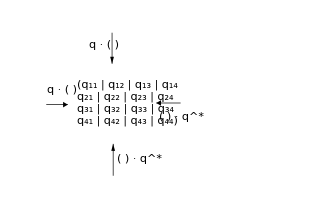

The meaning of the compound multiplications across columns and rows is extracting and affecting individual components of quaternions embedded from the previous rotations of the tensor. The moment of inertia tensor can always be reduced to its principal axes in diagonal form. In a matrix representation of a quaternion, the diagonal of the matrix contains the repeated scalar (real) part of the quaternion. (For any quaternion q there exist quaternion p such that qp is scalar.) The principal moment of inertia, on the other hand, has on its diagonal three different scalars in general case, which gives origin to three different quaternions that are embedded and independently shuffled across-columns/rows during rotations.

## References

[1] Eberly, David H. with a contrib. by Shoemake, Ken - Game Physics, Morgan Kaufmann, 2004, Chapter 10 "Quaternions", pp. 507-544, http://books.google.se/books?id=a9SzFHPJ0mwC

[2] Shoemake, Ken - Uniform random rotations, in: D. Kirk (Ed.), Graphics Gems III, Academic Press, London, 1992, pp. 124-132, http://books.google.se/books?id=xmW_u3mQLmQC

[3] Shoemake, Ken - Quaternions, Department of Computer and Information Science, University of Pennsylvania, 2005-10-07, downloaded from C+MS course CS171 at Caltech: 
http://courses.cms.caltech.edu/cs171/quatut.pdf